```mathematica
(*
Shows that 𝒸Lim[m] satisfies the requirements of good 𝒸Lim[m] function:
𝒸Lim[m] > 𝒸[m];
κLim[m] smooth;
𝒸Lim[0]=0;
κLim[0]>κMaxInf;
κLim'[m] ≤ 0;
*)
Print["Running doApndxcLim"];
```

```mathematica
(* This cell contains generic setup stuff to prepare for execution of the programs *)
ClearAll["Global`*"]; ParamsAreSet = False;
If[$VersionNumber < 6,(*then*) Print["These programs require Mathematica version 6 or greater."]; Abort[]];
(* If running from Notebook front end, set directory to Notebook's directory *)
If[Length[$FrontEnd] > 0, NBDir = SetDirectory[NotebookDirectory[]]];
(* If not running from Notebook front end, set directory manually *)
If[Length[$FrontEnd] == 0,SetDirectory["/Volumes/Data/Work/BufferStock/BufferStockTheory/Latest/Code/Mathematica/Results/BufferStockTheory"]];
SaveFigs = True;

HomeDir = Directory[];
CodeDir = HomeDir<>"/../../CoreCode";
CDToHomeDir := SetDirectory[HomeDir];
CDToCodeDir := SetDirectory[HomeDir<>"/../../CoreCode"];
CDToCodeDir;
<< SetupModelSolutionRoutines.m;
<< SetParamsToBaselineVals.m;
CDToHomeDir;
```

```mathematica
SetupGrids;
SetupShocks;
ConstructLastPeriod;
```

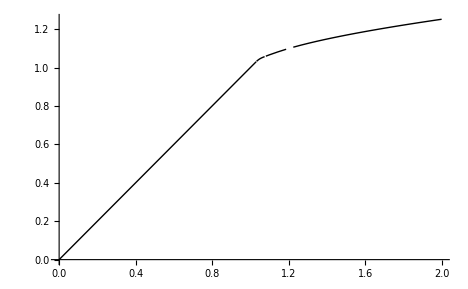

```mathematica
Print[Plot[𝒸Lim[m],{m,0,2}]];
```

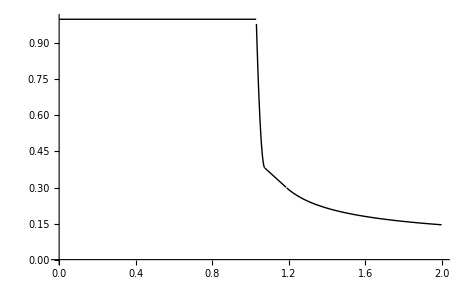

```mathematica
Print[Plot[κLim[m],{m,0,2}]];
```